```mathematica
f[n_, x_]:=n/(π(1 + x^2)n^2);
Plot[Evaluate[Table[f[n, x],{n,1, 3}]],{x,-10,10}, PlotRange->All, PlotLabel->Style["Secuencia delta ϕ_n(x)", Black, FontSize->14], PlotLegends->{"n=3", "n=2", "n=1"}]
```

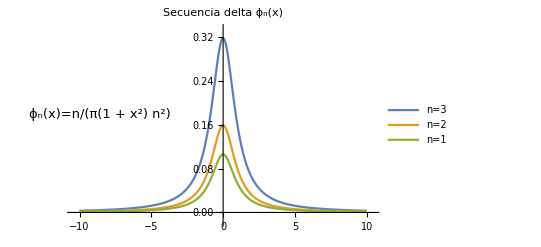

```mathematica
g[n_, x_]:=(n  Exp[-n^2 x^2])/(√π);
Plot[Evaluate[Table[g[n, x],{n,1, 3}]],{x,-4,4}, PlotRange->All, PlotLabel->Style["Secuencia delta ϕ_n(x)", Black, FontSize->14], PlotLegends->{"n=1", "n=2", "n=3"}]
```

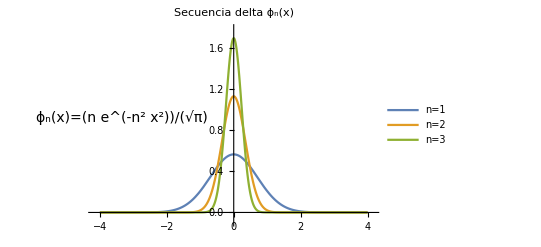

```mathematica
h[n_, x_]:=(Sin[n x])^2/(n π x^2);
Plot[Evaluate[Table[h[n, x],{n,1, 3}]],{x,-4,4}, PlotRange->All, PlotLabel->Style["Secuencia delta ϕ_n(x)", Black, FontSize->14], PlotLegends->{"n=1", "n=2", "n=3"}]
```

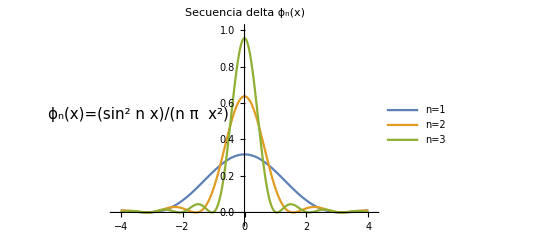

```mathematica
D[g[n,x],x]
D[g[3,x],x]
```

-(2 ⅇ^(-n^2 x^2) n^3 x)/(√π)

-(54 ⅇ^(-9 x^2) x)/(√π)

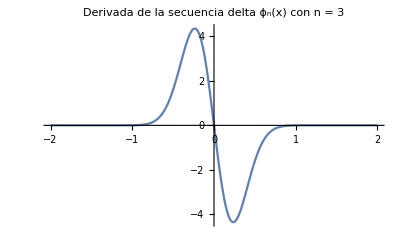

```mathematica
Plot[-(54 ⅇ^(-9 x^2) x)/(√π),{x,-2,2}, PlotLabel->Style["Derivada de la secuencia delta ϕ_n(x) con n = 3", Black, FontSize->14],PlotRange->Full]
```